```mathematica
(* G = c = M = 1 => r_s = 2 | BL Coords*)
coords = {t, r, θ, ϕ};
n=Length[coords];
tt = 2 r / Σ - 1;
rr = Σ/Δ;
θθ=Σ;
φφ=(Δ+(2r (r^2+a^2))/Σ) Sin[θ]^2;
tφ=−4a r Sin[θ]^2/Σ;
gdd={{tt,0,0,tφ},{0,rr,0,0},{0,0,θθ,0},{tφ,0,0,φφ}};
Simplify[gdd]//MatrixForm
guu=Simplify[Inverse[gdd]];
guu//MatrixForm
```

(-1+(2 r)/Σ | 0 | 0 | -(4 a r Sin[θ]^2)/Σ
0 | Σ/Δ | 0 | 0
0 | 0 | Σ | 0
-(4 a r Sin[θ]^2)/Σ | 0 | 0 | (Δ+(2 r (a^2+r^2))/Σ) Sin[θ]^2)

(-(Σ (2 a^2 r+2 r^3+Δ Σ))/(2 a^2 r (2 r+Σ)-(2 r-Σ) (2 r^3+Δ Σ)-8 a^2 r^2 Cos[2 θ]) | 0 | 0 | (4 a r Σ)/(-2 a^2 r (2 r+Σ)+(2 r-Σ) (2 r^3+Δ Σ)+8 a^2 r^2 Cos[2 θ])
0 | Δ/Σ | 0 | 0
0 | 0 | 1/Σ | 0
(4 a r Σ)/(-2 a^2 r (2 r+Σ)+(2 r-Σ) (2 r^3+Δ Σ)+8 a^2 r^2 Cos[2 θ]) | 0 | 0 | -(Σ (-2 r+Σ) Csc[θ]^2)/(-2 a^2 r (2 r+Σ)+(2 r-Σ) (2 r^3+Δ Σ)+8 a^2 r^2 Cos[2 θ]))

```mathematica
a=.;
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 r+a^2;
christoffels:=christoffels=Simplify[Table[(1 / 2)* Sum[(guu[[i,s]])*(D[gdd[[s,j]],coords[[k]]]+D[gdd[[s,k]],coords[[j]]]−D[gdd[[j,k]],coords[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]

listchristoffels:=Table[If[UnsameQ[christoffels[[i,j,k]],0], {ToString[Γ[i,j,k]], christoffels[[i,j,k]]}], {i, 1, n}, {j, 1, n}, {k, 1, j}]

TableForm[Partition[DeleteCases[Flatten[listchristoffels],Null],2],TableSpacing->{2,2}]

geodesic:=geodesic=Simplify[Table[−Sum[christoffels[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]

listgeodesic:=Table[{"d/dλ"ToString[coords[[i]]'],"=", geodesic[[i]]}, {i, 1, n}]

TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | ((r^2-a^2 Cos[θ]^2) (a^4+3 a^2 (-2+r) r+2 r^4+a^2 (a^2+r (6+r)) Cos[2 θ]))/(2 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))
Γ[1, 3, 1] | -(a^2 r Cos[θ] (a^4+2 (-8+r) r^3+a^2 r (-14+3 r)+a^2 (a^2+(-2+r) r) Cos[2 θ]) Sin[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))
Γ[1, 4, 2] | (2 a (-r^2 (a^2+3 r^2)+a^2 (a^2-r^2) Cos[θ]^2) Sin[θ]^2)/(2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ]))
Γ[1, 4, 3] | (4 a^3 r (a^2+(-2+r) r) Cos[θ] Sin[θ]^3)/(2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ]))
Γ[2, 1, 1] | -((a^2+(-2+r) r) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 2, 2] | ((a^2-r) r-a^2 (-1+r) Cos[θ]^2)/((a^2+(-2+r) r) (r^2+a^2 Cos[θ]^2))
Γ[2, 3, 2] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[2, 3, 3] | -(r (a^2+(-2+r) r))/(r^2+a^2 Cos[θ]^2)
Γ[2, 4, 1] | (2 a (a^2+(-2+r) r) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 4, 4] | -((a^2+(-2+r) r) (-a^2 r^2+r^5+a^2 (a^2+r^2+2 r^3) Cos[θ]^2+a^4 (-1+r) Cos[θ]^4) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 1, 1] | -(2 a^2 r Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 2, 2] | (a^2 Cos[θ] Sin[θ])/((a^2+(-2+r) r) (r^2+a^2 Cos[θ]^2))
Γ[3, 3, 2] | r/(r^2+a^2 Cos[θ]^2)
Γ[3, 3, 3] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[3, 4, 1] | (2 a r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 4, 4] | (Cos[θ] Sin[θ] (-(r^2+a^2 Cos[θ]^2)^2 (a^2-2 r+r^2+(2 r (a^2+r^2))/(r^2+a^2 Cos[θ]^2))-2 a^2 r (a^2+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[4, 2, 1] | (2 a r^2-2 a^3 Cos[θ]^2)/(2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ]))
Γ[4, 3, 1] | -(4 a r (a^2+(-2+r) r) Cot[θ])/(2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ]))
Γ[4, 4, 2] | (2 a^2 r^3-a^2 r^4-2 r^6+r^7-a^2 r (2 a^2+r^2 (2+3 r-3 r^2)) Cos[θ]^2+a^4 (a^2+r (2-2 r+3 r^2)) Cos[θ]^4+a^6 (-1+r) Cos[θ]^6-8 a^2 r^3 Sin[θ]^2+2 a^4 r Sin[2 θ]^2)/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))
Γ[4, 4, 3] | (Cot[θ] (a^4 r^2 (4+3 a^2-6 r+3 r^2) Cos[θ]^4+a^6 (a^2+(-2+r) r) Cos[θ]^6+r^2 ((-2+r) r^5+a^4 (6+r)+a^2 r^2 (2+r+r^2)-a^2 (6+r) (a^2+r^2) Cos[2 θ])+a^2 r Cos[θ]^2 (a^2 r (-4+3 r^2)+r^3 (4-6 r+3 r^2)+2 a^2 (a^2+r^2) Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))

d/dλ t' | =
(-2 a^2 r θ' (-2 (a^4+2 (-8+r) r^3+a^2 r (-14+3 r)+a^2 (a^2+(-2+r) r) Cos[2 θ]) Sin[2 θ] t'+8 a (a^2+(-2+r) r) Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ]) Sin[θ]^3 ϕ')+r' ((3 a^6-6 a^4 r+3 a^4 r^2+24 a^2 r^3-8 a^2 r^4-8 r^6+4 a^2 (a^4+a^2 r^2-6 r^3) Cos[2 θ]+a^4 (a^2+r (6+r)) Cos[4 θ]) t'-16 a ((-r^4 (a^2+3 r^2)+a^4 (a^2-r^2) Cos[θ]^4) Sin[θ]^2-a^2 r^4 Sin[2 θ]^2) ϕ'))/(4 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ]))) | d/dλ r'
= | (((r^2+a^2 Cos[θ]^2)^2 (r (-a^2+r)+a^2 (-1+r) Cos[θ]^2) (r')^2)/(a^2+(-2+r) r)+(a^2+(-2+r) r) (-r^2+a^2 Cos[θ]^2) (t')^2+2 a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] r' θ'+r (a^2+(-2+r) r) (r^2+a^2 Cos[θ]^2)^2 (θ')^2-4 a (a^2+(-2+r) r) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2 t' ϕ'+(a^2+(-2+r) r) (-a^2 r^2+r^5+a^2 (a^2+r^2+2 r^3) Cos[θ]^2+a^4 (-1+r) Cos[θ]^4) Sin[θ]^2 (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dλ θ' | =
(-(a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (r')^2)/(a^2+(-2+r) r)+a^2 r Sin[2 θ] (t')^2-2 r (r^2+a^2 Cos[θ]^2)^2 r' θ'+a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (θ')^2-4 a r (a^2+r^2) Sin[2 θ] t' ϕ'-Cos[θ] Sin[θ] (-(r^2+a^2 Cos[θ]^2)^2 (a^2-2 r+r^2+(2 r (a^2+r^2))/(r^2+a^2 Cos[θ]^2))-2 a^2 r (a^2+r^2) Sin[θ]^2) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3) | d/dλ ϕ'
= | -(2 (θ' (-2 a r (a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ] t'+((a^2 r^2 (a^2 (-4+3 r^2)+r^2 (4-6 r+3 r^2)) Cos[θ]^2+a^4 r^2 (4+3 a^2-6 r+3 r^2) Cos[θ]^4+a^6 (a^2+(-2+r) r) Cos[θ]^6+r^2 ((-2+r) r^5+a^4 (6+r)+a^2 r^2 (2+r+r^2)-a^2 (6+r) (a^2+r^2) Cos[2 θ])) Cot[θ]+2 a^4 r (a^2+r^2) Cos[θ]^3 Sin[θ]) ϕ')+r' ((2 a r^4-2 a^5 Cos[θ]^4) t'+(2 a^2 r^3-a^2 r^4-2 r^6+r^7-a^2 r (2 a^2+r^2 (2+3 r-3 r^2)) Cos[θ]^2+a^4 (a^2+r (2-2 r+3 r^2)) Cos[θ]^4+a^6 (-1+r) Cos[θ]^6-8 a^2 r^3 Sin[θ]^2+2 a^4 r Sin[2 θ]^2) ϕ')))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (2+a^2-2 r+r^2) Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))

```mathematica
christoffels[[4,4,3]]/.{r^2+a^2 Cos[θ]^2->sg,
r^2-2 r+a^2->dl}
```

(Cot[θ] (a^4 r^2 (4+3 a^2-6 r+3 r^2) Cos[θ]^4+a^6 (a^2+(-2+r) r) Cos[θ]^6+r^2 ((-2+r) r^5+a^4 (6+r)+a^2 r^2 (2+r+r^2)-a^2 (6+r) (a^2+r^2) Cos[2 θ])+a^2 r Cos[θ]^2 (a^2 r (-4+3 r^2)+r^3 (4-6 r+3 r^2)+2 a^2 (a^2+r^2) Sin[θ]^2)))/(sg (2 a^2 (2+dl) r^2 Cos[θ]^2+a^4 (a^2+(-2+r) r) Cos[θ]^4+r^2 ((-2+r) r^3+a^2 (4+r^2)-8 a^2 Cos[2 θ])))

```mathematica
Sol[λmax_, vel_, pos_]:=Block[{v, x, i, vt, tmp, soln}, x=pos;v=Join[{vt}, vel];tmp=gdd;tmp=tmp/.Table[coords[[i]]->x[[i]],{i,0,n}];tmp=v.(tmp.v);vts = Solve[tmp==norm,vt];v[[1]]=Last[vt/.vts];deq=Table[coords[[i]]''[λ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[λ],{i,1,n}],Table[coords[[i]]->coords[[i]][λ],{i,1,n}]]),{i,1,n}];deq=Join[deq,Table[coords[[i]]'[0]==v[[i]],{i,1,n}],Table[coords[[i]][0]==x[[i]],{i,1,n}]];soln=NDSolve[deq,coords,{λ,0,λmax}];soln]

sphToCart[soln_]:=Block[{xs,ys,zs},xs=r[λ]Sin[θ[λ]]Cos[ϕ[λ]]/.soln;ys=r[λ]Sin[θ[λ]]Sin[ϕ[λ]]/.soln;zs=r[λ]Cos[θ[λ]]/.soln;{xs,ys,zs}]

unorm[solni_,λval_]:=Block[{xα,vα},
xα=Table[coords[[i]][λ]/.solni,{i,1,n}]//Flatten;
vα=D[xα,λ];
xα=xα/.λ->λval;
vα=vα/.λ->λval;
vα.((gdd/.Table[coords[[i]]->xα[[i]],{i,1,n}]).vα)]

coordlist[λin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][λin]/.soln//First]},{i,1,n}]
```

|  |  | u.u values
λ= | 0 | → | -1.01373×10^-17
λ= | 40 | → | -9.40859×10^-9
λ= | 80 | → | -1.16274×10^-8
λ= | 120 | → | 3.93938×10^-9
λ= | 160 | → | 4.04889×10^-9
λ= | 200 | → | 8.28937×10^-9

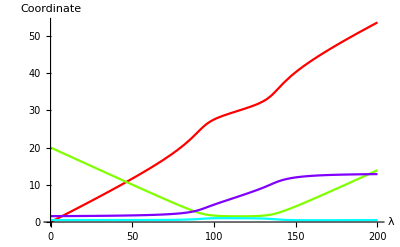

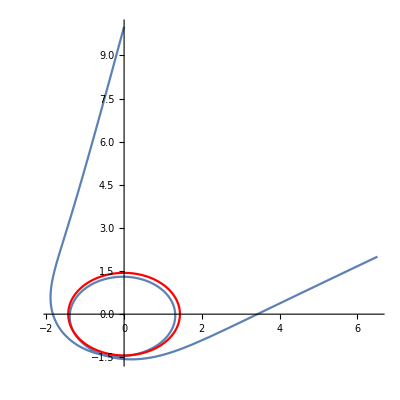

-Graphics3D-

```mathematica
norm=0; (* Set to -1 for Timelike *)
a=0.9;
rplus=1 + Sqrt[1 - a ^2]; (* Outer EH *)
λmax=200;
BH=PolarPlot[rplus, {θ, 0, 2Pi}, PlotStyle->Hue[0]];
sol=Sol[λmax,{−.2,0,.002},{0,20,Pi/6,Pi/2}];
cartsol=sphToCart[sol];
(* Calculates norm(U) at intervals of λ, should be == norm *)
Join[{{"","","","u.u values"}},Table[{"λ=",ToString[i],"→",unorm[sol,i]},{i,0,λmax,λmax/5}]]//TableForm
(* Plots *)
Plot[Evaluate[Table[coords[[i]][λ]/.sol,{i,1,n}]],{λ,0,λmax},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],AxesLabel->{"λ","Coordinate"}]
geod=ParametricPlot[Evaluate[{cartsol[[1]],cartsol[[2]]}// Flatten],{λ,0,λmax}];
Show[geod, BH, AspectRatio->1]
BH3D=SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{φ,0,2 Pi}];
geof3D=ParametricPlot3D[Evaluate[Re[cartsol]//Flatten],{λ,0,λmax},PlotRange->All];
Show[geof3D,BH3D]
```